# Sending Queries to IBM QPUs

In the Wolfram Quantum Framework a quantum circuit is a single symbolic object: you can simulate it exactly and send that same object to a real IBM Quantum processing unit (QPU). This tutorial walks the full path: connect to the IBM Quantum Platform, build and check a circuit, inspect it as OpenQASM (the portable text format QPUs read), submit it to hardware with IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol, and hold the hardware counts up against the exact result.

Building and checking run locally with no account. The hardware cells need an IBM Quantum account and are marked so you can read the tutorial without running them. For help, write to quantum@wolfram.com.

```mathematica
<< Wolfram`QuantumFramework`
```

## Connecting to the IBM Quantum Platform

Create an account at quantum.cloud.ibm.com. From the dashboard you need two things: an IAM API key (the long secret string shown once when you create the key, not the key's display name) and the instance CRN (a crn:v1:… string identifying your instance).

The API key is a secret and is stored in your encrypted system credential store. The CRN is read from a local symbol that the connection consults when it builds the request headers, so set both before connecting:

```mathematica
api = "XXX";
LocalSymbol["ibm_crn"] = "XXX";
```

Loading the Wolfram Quantum Framework registers the IBM Quantum Platform service automatically, so ServiceConnectpaclet:ref/ServiceConnect recognizes the "IBMQuantumPlatform" name directly:

```mathematica
ibm = ServiceConnect["IBMQuantumPlatform", "New", Authentication -> {"apikey" -> api}]
```

A connected service object lists the QPUs your account can reach through "Backends". Submitting and retrieving jobs is handled for you by IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol and the IBMJobpaclet:Wolfram/QuantumFramework/ref/IBMJobWolfram/QuantumFramework Package Symbol handle, shown below. List the available backends:

```mathematica
ibm["Backends"]
```

Before spending QPU time, you can inspect a backend's live calibration as an error map with ibm["ErrorMap", "Backend" -> "ibm_fez"] (and read the numbers through ibm["DeviceModel", …]); see the IBM error map tutorialpaclet:Wolfram/QuantumFramework/tutorial/IBMQuantumErrorMap.

## Building and checking a circuit

Build the circuit in the Wolfram Language first, so you have an exact reference to compare the hardware against. This example prepares a three-qubit GHZ state GHZ=1/(√2)(000+111), applies a quantum Fourier transform and measures all three qubits. The transform turns the GHZ entanglement into a definite interference pattern across the eight outcomes, and that structure is exactly what device noise erodes, which makes the circuit a sensitive benchmark:

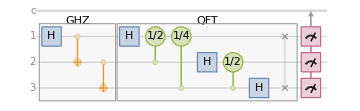

```mathematica
qc = QuantumCircuitOperator[{"GHZ", "Fourier"[3], {1, 2, 3}}];
qc["Diagram"]
```

Because the circuit is small, plot its exact output distribution: the noiseless ground truth a QPU run approximates, and the reference we overlay with the hardware counts:

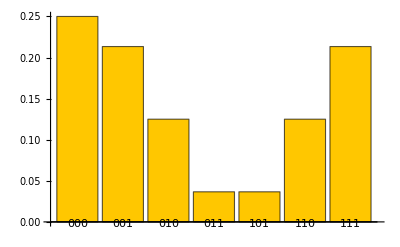

```mathematica
qc[]["ProbabilityPlot"]
```

Before spending QPU time, you can sample the circuit on a local noiseless simulator. QuantumCircuitOperatorpaclet:Wolfram/QuantumFramework/ref/QuantumCircuitOperatorWolfram/QuantumFramework Package Symbol's "Qiskit" interface runs through a local Qiskit Aer simulator when no provider is given, returning a QuantumMeasurementpaclet:Wolfram/QuantumFramework/ref/QuantumMeasurementWolfram/QuantumFramework Package Symbol whose statistics converge to the exact distribution as the shot count grows (this needs the Python Qiskit stack):

```mathematica
qc["Qiskit"]["Shots" -> 4096]["ProbabilityPlot"]
```

## Inspecting the circuit as OpenQASM

A QPU does not read a Wolfram Language expression: the circuit is sent as OpenQASM. QuantumQASMpaclet:Wolfram/QuantumFramework/ref/QuantumQASMWolfram/QuantumFramework Package Symbol is the single hub for it. Called on a circuit with no extra arguments it emits OpenQASM 3.0 natively, in pure Wolfram Language with no external dependency, serializing the circuit exactly as built. Measurements become classical-bit assignments:

```mathematica
QuantumQASM[qc]
```

OPENQASM 3.0;
qubit[3] q;
bit[3] c;
U(1.5707963267948966, 0., 3.141592653589793) q[0];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[1];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[1] q[2];
U(1.5707963267948966, 0., 3.141592653589793) q[0];
ctrl(1) @ negctrl(0) @ U(0., 0., 1.5707963267948966) q[1] q[0];
ctrl(1) @ negctrl(0) @ U(0., 0., 0.7853981633974483) q[2] q[0];
U(1.5707963267948966, 0., 3.141592653589793) q[1];
ctrl(1) @ negctrl(0) @ U(0., 0., 1.5707963267948966) q[2] q[1];
U(1.5707963267948966, 0., 3.141592653589793) q[2];
swap q[0] q[2];
c[0] = measure q[0];
c[1] = measure q[1];
c[2] = measure q[2];

The hub is also an importer: handing OpenQASM source (or a .qasm file) back to QuantumCircuitOperatorpaclet:Wolfram/QuantumFramework/ref/QuantumCircuitOperatorWolfram/QuantumFramework Package Symbol reconstructs the circuit, again with no external dependency. The round trip recovers a circuit equal to the original:

```mathematica
QuantumCircuitOperator[QuantumQASM[qc]] == qc
```

True

OpenQASM 3.0 is the native and recommended target. For older toolchains that still require the legacy qelib1.inc gate set, pass "Version" -> 2 to emit OpenQASM 2.0. This path renders through Qiskit, so it needs the Python Qiskit stack configured:

```mathematica
QuantumQASM[qc, "Version" -> 2]
```

## Running on hardware

With an active connection, IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol is the one call that runs a circuit on a QPU. It transpiles the circuit against the backend's own error-aware Target (per-instruction error and duration), submits it through the SamplerV2 primitive, and returns immediately with an asynchronous IBMJobpaclet:Wolfram/QuantumFramework/ref/IBMJobWolfram/QuantumFramework Package Symbol handle while the job sits in the queue. There is no manual OpenQASM, no raw request and no hex decoding of the classical register: the handle carries the per-bit to qubit map captured at transpile time, so results come back already in the Wolfram Language qubit order.

```mathematica
job = IBMJobSubmit[qc, "ibm_fez"]
```

The handle reports the job's status. Poll it while the job is queued, or pass "Wait" -> True to IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol to block until the job reaches a terminal status:

```mathematica
job["Status"]
```

Refresh the handle to pull a fresh snapshot from the service. Once the status is "Completed", applying the handle returns the measurement reconstructed from the hardware counts:

```mathematica
qpu = job["Refresh"][]
```

The same handle keeps every response IBM returns under "Raw" and exposes curated accessors on top, so the run's metadata is one query away. For example, the billed quantum runtime:

```mathematica
job["QuantumSeconds"]
```

## Choosing the qubit layout

By default IBMJobSubmitpaclet:Wolfram/QuantumFramework/ref/IBMJobSubmitWolfram/QuantumFramework Package Symbol lays the circuit out for you: it runs the backend's error-aware preset transpiler, which picks the physical qubits and the routing. Two options hand that choice back to you.

"InitialLayout" pins the physical qubits. Give it the device qubit indices (0-indexed, the same numbering the backend and its error map use) that the circuit's logical qubits map onto in order. The circuit is still transpiled to the backend's native gates and routed, so it stays hardware-valid, but it runs on the qubits you chose, and the counts still return in the original logical-qubit order:

```mathematica
job = IBMJobSubmit[qc, "ibm_fez", "InitialLayout" -> {12, 13, 14}]
```

"Transpile" -> False submits the circuit exactly as given, skipping layout and routing. Use it for a circuit that is already in the backend's native gate set on physical qubits, for example one you transpiled yourself to control every pass. Here the circuit is compiled with QiskitCircuitpaclet:Wolfram/QuantumFramework/ref/QiskitCircuitWolfram/QuantumFramework Package Symbol's "Transpile" property (which itself takes an "InitialLayout") and handed straight to submission:

```mathematica
isa = QuantumCircuitOperator[
   qc["Qiskit"]["Transpile", "Provider" -> "IBMProvider", "Backend" -> "ibm_fez", "InitialLayout" -> {12, 13, 14}]];
job = IBMJobSubmit[isa, "ibm_fez", "Transpile" -> False]
```

The SamplerV2 primitive only accepts a hardware-ready (ISA) circuit, so with "Transpile" -> False a circuit that is not already native for the backend is rejected by the QPU rather than silently re-laid-out. When you only need to fix which qubits are used, "InitialLayout" is the safer choice: it hands you that control while still producing a valid circuit.

## Comparing exact and hardware results

qpu is the hardware measurement returned by the handle; the circuit qc gives the exact, noiseless reference. Take the corresponding Wolfram Language measurement:

```mathematica
wl = qc[];
```

Putting the two distributions side by side shows how much of the interference pattern survives the hardware. Each QuantumMeasurementpaclet:Wolfram/QuantumFramework/ref/QuantumMeasurementWolfram/QuantumFramework Package Symbol exposes its outcome distribution through "Probabilities"; sorting both by outcome and overlaying them, the dominant 000, 001 and 111 peaks and the all-but-forbidden 100 still come through, while decoherence erodes the contrast and pulls the rest toward a uniform distribution:

```mathematica
BarChart[Transpose[Values @* KeySort /@ {wl["Probabilities"], qpu["Probabilities"]}],
    AspectRatio -> 1/2, Frame -> True, ChartLegends -> {"Exact WL", "QPU ibm_fez"},
    PlotLabels -> Keys[wl["Probabilities"]]]
```

The differences are not in the queries but in device noise: each shot passes through a deep transpiled circuit on superconducting hardware, and the noise varies from job to job.

Related Guides

WolframQuantumComputationFrameworkpaclet:Wolfram/QuantumFramework/guide/WolframQuantumComputationFramework

Related Tech Notes

IBMQuantumErrorMappaclet:Wolfram/QuantumFramework/tutorial/IBMQuantumErrorMap ▪ QPUServiceConnectpaclet:Wolfram/QuantumFramework/tutorial/QPUServiceConnect ▪ GettingStartedpaclet:Wolfram/QuantumFramework/tutorial/GettingStarted

## Metadata

### Categorization

Tutorial

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/SendingQueriesToIBMQPUs

### Keywords

IBM Quantum

QPU

OpenQASM

Qiskit

ServiceConnect

IBMJobSubmit

IBMJob

sampler

SamplerV2

transpile

quantum hardware